newtonRaphson Method Function Called for f(x)=-2+ⅇ^x_+3 x_-x_^2 Starting value p= 0.

Condition Exists at 3.

# | p
0 | 0.
1 | 0.25
2 | 0.25752494504574
3 | 0.2575302854371955

p= 0.2575302854371955

Through Built In Routines: {x→0.25753}

newtonRaphson Method Function Called for f(x)=2 Cos[2 x_] x_-(1+x_)^2 Starting value p= -2.

Condition Exists at 4.

# | p
0 | -2.
1 | -2.239297869225592
2 | -2.192852038835903
3 | -2.191309816711106
4 | -2.191308011799723

p= -2.191308011799723

Through Built In Routines: {x→-2.19131}

newtonRaphson Method Function Called for f(x)=2 Cos[2 x_] x_-(1+x_)^2 Starting value p= -1.

Condition Exists at 4.

# | p
0 | -1.
1 | -0.813783025406316
2 | -0.7983458812221341
3 | -0.7981599890441817
4 | -0.7981599614057965

p= -0.7981599614057965

Through Built In Routines: {x→-0.79816}

newtonRaphson Method Function Called for f(x)=-1+3 x_+Cos[x_] x_-2 x_^2 Starting value p= 0.3

Condition Exists at 2.

# | p
0 | 0.3
1 | 0.2975246577465629
2 | 0.2975302336433776

p= 0.2975302336433776

Through Built In Routines: {x→0.29753}

newtonRaphson Method Function Called for f(x)=-1+3 x_+Cos[x_] x_-2 x_^2 Starting value p= 1.3

Condition Exists at 3.

# | p
0 | 1.3
1 | 1.258478412139689
2 | 1.256627023714742
3 | 1.256623322520362

p= 1.256623322520362

Through Built In Routines: {x→1.25662}

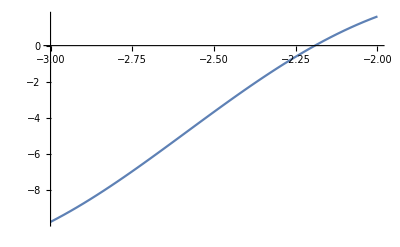
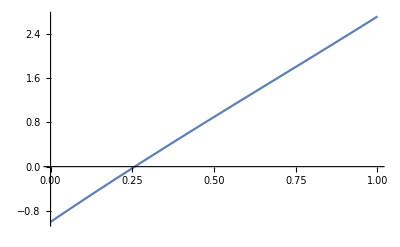
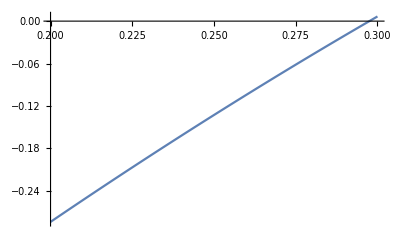
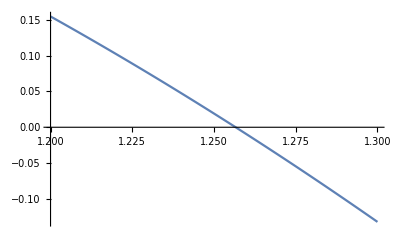
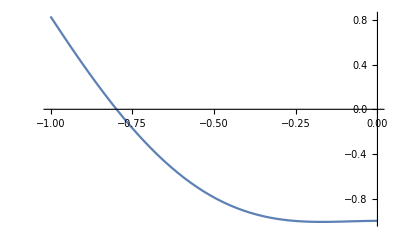
{{Null^13 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-},{□}}

```mathematica
(*   Aisha Muhammad Nawaz        L20-0921        BSCS SECTION 5E         Assignment #2         Numerical Computing*)

(*Making a function*){{newtonRaphsonMethod[a0_,b0_,err_,n_]:=
Module[{},

If[Abs[f[N[a0]]]<Abs[f[N[b0]]],
p=N[a0],p=N[b0]];
e=N[err];

Print ["newtonRaphson Method Function Called for f(x)=",f[x_]," Starting value p= ",p];
i=0;
output={{i,p}};
While [i<n,
p1=p-f[p] / f'[p];
output=Append[output,{i+1,p1}];
If[Abs[p1-p]<e,Print["Condition Exists at ", i+1, "."];Break[]];
p=p1;
i=i+1;
];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"#","p"}}],16]];
Print["p= ",NumberForm[p1,16]];
]




                                                                          (* TEST PROBLEM #1 *)
f[x_]:=Exp[x]-x^2+3x-2    (*Defining f(x)*)
newtonRaphsonMethod[0,1,10^-5,20] (*Calling the function newtonRaphson Method*)
Print["Through Built In Routines: ",FindRoot[f[x],{x,0,1}]]; (*Finding root through Built in Function*)
Plot[f[x],{x,0,1} ](*Plotting f(x) in given interval*)

                                                                            (* TEST PROBLEM #2 *)
f[x_]:=2x* Cos[2x]-(x+1)^2    

                                                          (*For interval -3≤x≤-2 *)
newtonRaphsonMethod[-3,-2,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,-3,-2}]];
Plot[f[x],{x,-3,-2} ]

                                                        (*For interval -1≤x≤0 *)
newtonRaphsonMethod[-1,0,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,-1,0}]];
Plot[f[x],{x,-1,0} ]

                                                                             (* TEST PROBLEM #3 *)
f[x_]:=x*Cos[x]-2x^2+3x-1   

                                                           (*For interval 0.2≤x≤0.3 *)
newtonRaphsonMethod[0.2,0.3,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,0.2,0.3}]];
Plot[f[x],{x,0.2,0.3} ]

                                                           (*For interval 1.2≤x≤1.3 *)
newtonRaphsonMethod[1.2,1.3,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,1.2,1.3}]];
Plot[f[x],{x,1.2,1.3} ]}, {□}}
```